```mathematica
L0 = 72/(√395);
E0 = √(210/237);
(*E0 = √0.905;*)
r0 = 10;
ϕ0 = 0;
(*Change this to 1.00027 and it goes mad, what the hell*)
(*M0 = 1.00026;*)
M0 = 1;
```

```mathematica
f[r_]:=1-(2M)/r
```

```mathematica
Veff[r_]:=f[r](1+L^2/r^2)
```

```mathematica
radialEq=r'[τ]^2+Veff[r[τ]]-En^2;
```

```mathematica
dradialEq = Simplify[D[radialEq,τ]] r[τ]^3/(r'[τ]2 r[τ]^3)//Expand;
```

```mathematica
(*Find U^r(0) for use as an initial condition when solving r'' later*)
ur = Solve[radialEq==0, r'[τ]];
(*ur0 = r'[τ]/.ur/.{M->M0, L->L0, En->E0, r[τ]->r0}*)
```

```mathematica
(*Define system of equations of motion*)
EqsOfM = {dradialEq==0, r[0]==r0, r'[0]==ur0[[1]], ϕ'[τ]==L/r[τ]^2, ϕ[0]==ϕ0}
```

Part::partd: Part specification ur0⟦1⟧ is longer than depth of object.

{(3 L^2 M)/r[τ]^4-L^2/r[τ]^3+M/r[τ]^2+r''[τ]==0,r[0]==10,r'[0]==ur0⟦1⟧,ϕ'[τ]==L/r[τ]^2,ϕ[0]==0}

```mathematica
(*Solve equations of motion over given range*)
solRange=2000
eomSol = Block[{M=M0, En=E0, L=L0}, NDSolve[EqsOfM, {r, ϕ}, {τ, 0, solRange}]]
```

2000

NDSolve::ndinnt: Initial condition ur0⟦1⟧ is not a number or a rectangular array of numbers.

NDSolve[{15552/(395 r[τ]^4)-5184/(395 r[τ]^3)+1/r[τ]^2+r''[τ]==0,r[0]==10,r'[0]==ur0⟦1⟧,ϕ'[τ]==72/(√395 r[τ]^2),ϕ[0]==0},{r,ϕ},{τ,0,2000}]

ReplaceAll::reps: {NDSolve[{15552/(395 r[«1»]^4)-5184/(395 r[«1»]^3)+1/r[τ]^2+r''[τ]==0,r[0]==10,r'[0]==ur0⟦1⟧,ϕ'[τ]==72/(√395 r[τ]^2),ϕ[0]==0},{r,ϕ},{τ,0,2000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0408163 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{15552/(395 r[«1»]^4)-5184/(395 r[«1»]^3)+1/r[0.0408163]^2+r''[0.0408163]==0,r[0]==10,r'[0]==ur0⟦1⟧,ϕ'[0.0408163]==72/(√395 r[«20»]^2),ϕ[0]==0},{r,ϕ},{0.0408163,0,2000}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0408163 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{39.3722/r[«1»]^4-13.1241/r[«1»]^3+1/r[«20»]^2+r''[0.0408163]==0.,r[0.]==10.,r'[0.]==ur0⟦1⟧,ϕ'[0.0408163]==3.62271/r[«20»]^2,ϕ[0.]==0.},«1»,{«1»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 40.8571 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

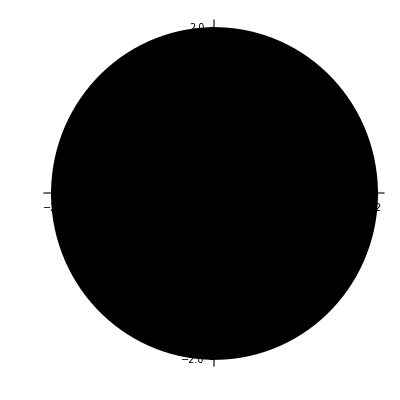

```mathematica
Show[ParametricPlot[Evaluate[{r[τ]Cos[ϕ[τ]],r[τ]Sin[ϕ[τ]]}/.eomSol],{τ,0,solRange}],
Graphics[Disk[{0,0}, 2M0]]]
```

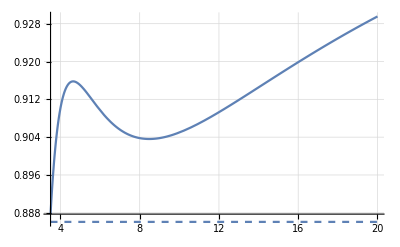

```mathematica
(**)
Block[{M=M0, En=E0, L=L0}, Show[Plot[Veff[r],{r,3.5,20},PlotRange->All, GridLines->Automatic], Plot[En^2, {r, 3.5, 20}, PlotStyle->Dashed]]]
```

```mathematica
Manipulate[
ur0 = r'[τ]/.ur/.{M->M0, L->L0, En->E0, r[τ]->r0};

EqsOfM = {dradialEq==0, r[0]==r0, r'[0]==ur0[[1]], ϕ'[τ]==L/r[τ]^2, ϕ[0]==ϕ0};

eomSol = Block[{M=M0, En=E0, L=L0}, NDSolve[EqsOfM, {r, ϕ}, {τ, 0, solRange}]];

VeffPlot = Block[{M=M0, En=E0, L=L0},Show[Plot[Veff[r],{r,3.5,40},PlotRange->All, GridLines->Automatic],Plot[En^2, {r, 3.5, 20}, PlotStyle->Dashed]]];

orbitPlot=ParametricPlot[Evaluate[{r[τ]Cos[ϕ[τ]],r[τ]Sin[ϕ[τ]]}/.eomSol],{τ,0,solRange}];

GraphicsGrid[{{orbitPlot},{VeffPlot}}]



,{{E0, √(217/237)},√0.905,√0.97}, {{solRange, 500}, 100, 1500}, {{r0, 7.2}, 6.5, 11.5}, {{L0, 72/(√395)}, 2√3, 4√3}]
```

```mathematica
(*Working to control the orbit directly with the geometric parameters (eccentricity and semilatus rectum) rather than the energy and angular momentum. Also set up to have high enough precision to come close to the separatrix and have some whirl orbits. Very happy.*)
(*Next steps are to explore the phase space of e and p and get some cool exmaples of each region, clean up this notebook in general (both to make it nicer and think through the design and hopefully speed it up a bit),try to move ombine the two methods into one notebook, or at least put a manipulate in the Differential Geometry method notebook to confirm it works the same.*)
e=0.5
Manipulate[
p=6.00000001+N[2, 10]e;
E0=√(((p-2-2e)(p-2+2e))/(p(p-3-e^2)));
L0=√((p^2 M0^2)/(p-3-e^2));
r0=p;
ur0 = r'[τ]/.ur/.{M->M0, L->L0, En->E0, r[τ]->r0};

EqsOfM = {dradialEq==0, r[0]==r0, r'[0]==ur0[[1]], ϕ'[τ]==L/r[τ]^2, ϕ[0]==ϕ0};

eomSol = Block[{M=M0, En=E0, L=L0}, NDSolve[EqsOfM, {r, ϕ}, {τ, 0, solRange}]];

VeffPlot = Block[{M=M0, En=E0, L=L0},Show[Plot[Veff[r],{r,3.5,40},PlotRange->All, GridLines->Automatic],Plot[En^2, {r, 3.5, 20}, PlotStyle->Dashed]]];

orbitPlot=ParametricPlot[Evaluate[{r[τ]Cos[ϕ[τ]],r[τ]Sin[ϕ[τ]]}/.eomSol],{τ,0,solRange}];

GraphicsGrid[{{orbitPlot},{VeffPlot}}]
, {{solRange, 500}, 10, 1500},{e,N[0.7, 10], 0.95}, {{p, 9}, 6, 12}]
```

0.5